# Quantitative Analysis of Rocky

* A good portion of this code is borrowed from Paul’s notebooks. We take minimal credit, beyond how we put the snippets together. *

Our transfer function overall:
Note: Distance Control is actually Kd/s + Kv

-Graphics-

```mathematica
(* Setting up individual transfer functions *)
Subscript[G, MOTOR]= β α /(s+α);
Subscript[G, MOTORCONTROLLER]=Subscript[J, p]+Subscript[J, i]/s;
Subscript[G, CONTROLLEDMOTOR] = Factor[Subscript[G, MOTOR] Subscript[G, MOTORCONTROLLER]/(1+Subscript[G, MOTOR] Subscript[G, MOTORCONTROLLER])];
Subscript[G, ANGLECONTROLLER]=Subscript[K, p]+Subscript[K, i]/s;
Subscript[G, VELOCITYTOANGLE]=-s/(L s^2- g);
Subscript[G, Distance] = (Subscript[K, d]/s )+ Subscript[K, v];
```

```mathematica
(* Solving for E_theta[s], theta[s], and V[s] *)
eq1 =Error[s] == Subscript[θ, d][s]-θ[s] + V[s] Subscript[G, Distance];
eq2 = θ[s] == Error[s]*Subscript[G, ANGLECONTROLLER]*Subscript[G, CONTROLLEDMOTOR]*Subscript[G, VELOCITYTOANGLE];
eq3 = V[s] == Error[s]*Subscript[G, ANGLECONTROLLER] * Subscript[G, CONTROLLEDMOTOR];
sol = Solve[{eq1, eq2, eq3},{θ[s],V[s], Error[s]}][[1]] ;

(* New transfer function *)
Subscript[G, NEWSYSTEM]=  θ[s]/(Subscript[θ, d][s])/.sol;
Factor[θ[s]/(Subscript[θ, d][s])/.sol];
```

```mathematica
(* Plugging in parametres, and solving for poles *)
parameters = {g-> 98/10, L-> .045, α-> 14, β-> 1/400, Subscript[K, d]-> .11, Subscript[K, v]-> .11};
poles := Values[NSolve[Denominator[Subscript[G, NEWSYSTEM]]==0,s]/.parameters]
```

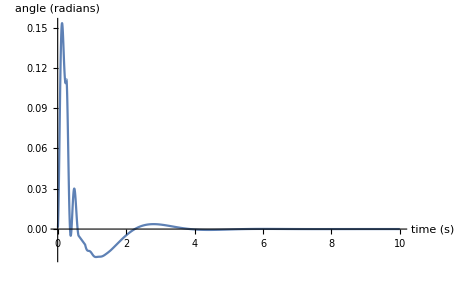

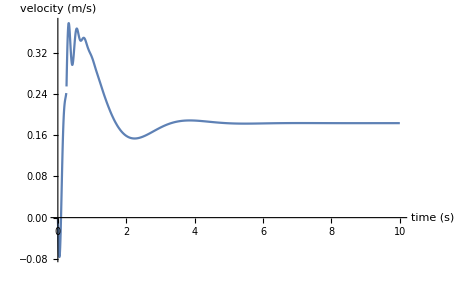

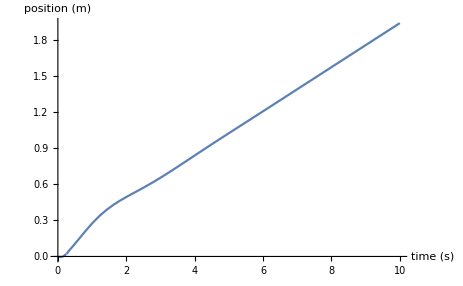

```mathematica
(* Graphing the response of the system in the time domain *)
controlParameters = {Subscript[J, p]->16,Subscript[J, i]->60,Subscript[K, p]->-80,Subscript[K, i]->-89};
thetaOutputResponse = InverseLaplaceTransform[LaplaceTransform[Subscript[θ, d][t],t,s](Subscript[G, TOTALSYSTEM]/.parameters /.controlParameters),s,t];
vOutputResponse = InverseLaplaceTransform[LaplaceTransform[Subscript[θ, d][t],t,s] ((Subscript[G, TOTALSYSTEM]/Subscript[G, VELOCITYTOANGLE])/.parameters /.controlParameters),s,t];
xOutputResponse = InverseLaplaceTransform[LaplaceTransform[Subscript[θ, d][t],t,s]/s((Subscript[G, TOTALSYSTEM]/Subscript[G, VELOCITYTOANGLE])/.parameters /.controlParameters),s,t];
Plot[thetaOutputResponse,{t,0,10},PlotRange-> All,AxesLabel->{"time (s)", "angle (radians)"}]
Plot[vOutputResponse,{t,0,10},PlotRange-> All,AxesLabel->{"time (s)", "velocity (m/s)"}]
Plot[xOutputResponse,{t,0,10},PlotRange-> All,AxesLabel->{"time (s)", "position (m)"}]
```

Using the Manipulate function to explore the behavior of the graphically.

```mathematica
Manipulate[ListPlot[ReIm[poles/.{Subscript[J, i]-> Ji, Subscript[K, i]-> Ki, Subscript[J, p]-> Jp, Subscript[K, p]-> Kp}],PlotRange-> {{-50,50},{-50,50}},PlotMarkers-> {Graphics[{Blue,Disk[]}],.025},AxesLabel->{"Re","Im"}],{Ji,-100, 100},{Ki,-600,600},{Kp,-600,600}, {Jp,-600,300}]

(* Values that we like: Kd = -.2, Kv = -.11, Ji = 80, Ki = -140, Kp - -36, Jp = 24 *)
```

```mathematica
DynamicModule[{Ji=60,Jp=16,Ki=-89,Kp=-80},ListPlot[ReIm[poles/.{Subscript[J, i]->Ji,Subscript[K, i]->Ki,Subscript[J, p]->Jp,Subscript[K, p]->Kp}],PlotRange->{{-50,50},{-50,50}},PlotMarkers->{Graphics[{Blue,Disk[]}],0.025},AxesLabel->{"Re","Im"}]]
```